# 2D 旋转

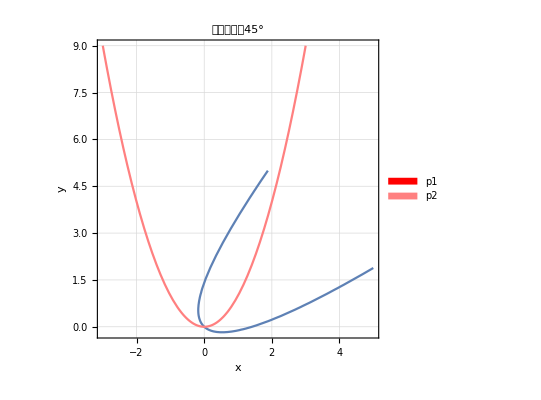

```mathematica
p1=ContourPlot[(x-y)^2==√2(x+y),{x,-1,5},{y,-1,5}];
p2=Plot[x^2,{x,-3,3},PlotStyle->{Pink}];
Legended[
Show[p1,p2,
PlotLabel->"抛物线旋转45°",
PlotRange->Automatic,
GridLines->Automatic,
AxesLabel->{"x","y"}
],
SwatchLegend[{Red,Pink},{"p1","p2"}]
]
```

### 旋转的椭圆

```mathematica
Manipulate[Graphics[{GeometricTransformation[Circle[{0,0},{a,b}],RotationTransform[θ]]},Axes->True,PlotRange->Max[a,b]],{a,1,5},{b,1,5},{θ,0,2π}]
```

```mathematica
Manipulate[Graphics[{Rotate[Circle[{0,0},{a,b}],θ]},Axes->True,PlotRange->Max[a,b]],{a,1,5},{b,1,5},{θ,0,2π}]
```

```mathematica
Manipulate[ParametricPlot[ReIm[(a Cos[x]+I b Sin[x])E^(I θ)],{x,0,2π},PlotRange->Max[a,b]],{a,1,5},{b,1,5},{θ,0,2π}]
```

```mathematica
Manipulate[ParametricPlot[{a Cos[x], b Sin[x]}.RotationMatrix[θ],{x,0,2π},PlotRange->Max[a,b]],{a,1,5},{b,1,5},{θ,0,2π}]
```

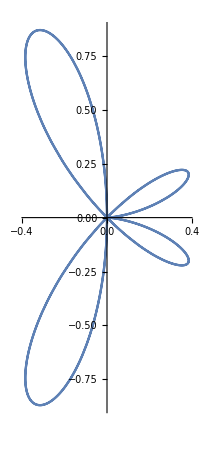

```mathematica
PolarPlot[Sin[x]Sin[5x],{x,0,2π}]
```

```mathematica
RevolutionPlot3D[Sin[x]Sin[3x],{x,0,2π},{θ,0,π}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{Sin[x]Sin[3x]Sin[x],Sin[x]Sin[3x]Cos[x]},{x,0,2π},{θ,0,π},RotationAction->"Clip",PlotPoints->30]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{Sin[x]Sin[3x]Cos[x],Sin[x]Sin[3x]Sin[x]},{x,0,2π},{θ,0,π},RotationAction->"Clip",PlotPoints->30]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[x]Sin[3x]Cos[x]Cos[θ],Sin[x]Sin[3x]Cos[x]Sin[θ],Sin[x]Sin[3x]Sin[x]},{x,0,2π},{θ,0,π},RotationAction->"Clip",PlotPoints->30]
```

-Graphics3D-

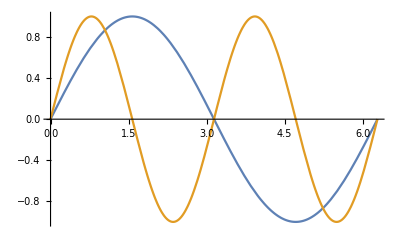

```mathematica
Plot[{Sin[x],Sin[2x]},{x,0,2π}]
```

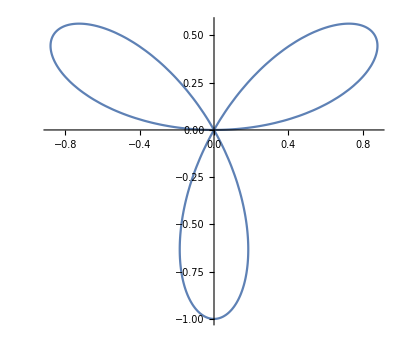

```mathematica
PolarPlot[Sin[3x],{x,0,π}]
```

```mathematica
SphericalPlot3D[Sin[x/4]Sin[y/4],{x,0,π},{y,0,3π},PlotPoints->50]
```

-Graphics3D-